```mathematica
1+ 1
```

2

```mathematica
MinGen[X_] := If[FreeQ[X,Around],Min[X],Min[#["Value"]& /@ X]];
MaxGen[X_] := If[FreeQ[X,Around],Max[X],Max[#["Value"]& /@ X]]
```

```mathematica
MinVal[L_, n_]:= MinGen[Transpose[L][[n]]];
```

```mathematica
MaxVal[L_, n_]:= MaxGen[Transpose[L][[n]]];
```

```mathematica
MinGen[{Around[1,0.1],Around[3,0.2]}]
```

1.

```mathematica
MinGen[{1,0.1,3,0.2}]
```

0.1

```mathematica
MyDnSample[L_, n_] := L[[#]]& /@Range[1,Length[L],n];
```

```mathematica
DataWithErrors[data_,n_, bins_]:=Around[#[[1]],#[[2]]] &/@ Transpose[{Mean[#],StandardDeviation[#]/Sqrt[bins]}]& /@ Partition[Sort[data,#1[[n]]<#2[[n]]&],bins];
```

```mathematica
DataWithErrors[data_, bins_]:=Around[#[[1]],#[[2]]] &/@ Transpose[{Mean[#],StandardDeviation[#]/Sqrt[bins]}]& /@ Partition[data,bins];
```

```mathematica
DataWithWeights[data_, bins_]:={Mean[#],Sqrt[bins]/StandardDeviation[#]}& /@ Partition[data,bins];
```

```mathematica
{dd,ww} =Transpose[DataWithWeights[Table[N[{x, Sin[Pi x]}],{x,-1,1,1/1000}],100]]
```

{{{-0.9505,-0.154247},{-0.8505,-0.450732},{-0.7505,-0.703096},{-0.6505,-0.886636},{-0.5505,-0.983386},{-0.4505,-0.983876},{-0.3505,-0.888056},{-0.2505,-0.705308},{-0.1505,-0.453519},{-0.0505,-0.157337},{0.0495,0.154247},{0.1495,0.450732},{0.2495,0.703096},{0.3495,0.886636},{0.4495,0.983386},{0.5495,0.983876},{0.6495,0.888056},{0.7495,0.705308},{0.8495,0.453519},{0.9495,0.157337}},{{344.691,111.331},{344.691,123.319},{344.691,155.178},{344.691,240.772},{344.691,674.834},{344.691,687.491},{344.691,242.249},{344.691,155.665},{344.691,123.517},{344.691,111.386},{344.691,111.331},{344.691,123.319},{344.691,155.178},{344.691,240.772},{344.691,674.834},{344.691,687.491},{344.691,242.249},{344.691,155.665},{344.691,123.517},{344.691,111.386}}}

```mathematica
dd[[;;5]]
```

{{-0.9505,-0.154247},{-0.8505,-0.450732},{-0.7505,-0.703096},{-0.6505,-0.886636},{-0.5505,-0.983386}}

```mathematica
ww[[;;5]]
```

{{344.691,111.331},{344.691,123.319},{344.691,155.178},{344.691,240.772},{344.691,674.834}}

```mathematica
Around[#[[1]],#[[2]]]& /@Transpose[{{m,m,m},{s,s,s}}]
```

{ms,ms,ms}

```mathematica
ttt=Transpose[{Table[RandomReal[],4],Table[RandomReal[],4],Table[RandomReal[],4]}]
```

{{0.264197,0.0974231,0.612537},{0.6036,0.41246,0.913453},{0.900021,0.486454,0.599607},{0.637353,0.573351,0.338789}}

```mathematica
Mean[#]& /@Partition[ttt,2]
```

{{0.433899,0.254942,0.762995},{0.768687,0.529902,0.469198}}

```mathematica
ttt[[;;3]]
```

{{0.264197,0.0974231,0.612537},{0.6036,0.41246,0.913453},{0.900021,0.486454,0.599607}}

```mathematica
Transpose[{{1,2},{a,b}, {x,y}}]
```

{{1,a,x},{2,b,y}}

```mathematica
test = Transpose[{ttt}];
```

```mathematica
Dimensions[ttt]
```

{4,3}

```mathematica
test =DataWithErrors[ArrayReshape[Sort[Table[RandomReal[],256]],{64,4}],4]
```

{{0.0410.011,0.0480.013,0.0510.013,0.0560.012},{0.1050.007,0.1070.007,0.1110.009,0.1150.011},{0.1630.007,0.1640.007,0.1680.008,0.1720.007},{0.2200.011,0.2230.011,0.2250.011,0.2310.010},{0.2860.014,0.2900.013,0.2930.013,0.2990.013},{0.3560.010,0.3610.010,0.3640.010,0.3690.009},{0.4200.011,0.4220.012,0.4280.011,0.4310.011},{0.4870.011,0.4950.010,0.4980.011,0.5010.011},{0.5490.008,0.5540.006,0.5600.010,0.5640.011},{0.6150.009,0.6170.009,0.6190.009,0.6230.009},{0.6640.008,0.6670.008,0.6700.006,0.6720.006},{0.7130.008,0.7160.009,0.7200.010,0.7230.010},{0.7720.010,0.7760.009,0.7790.009,0.7840.008},{0.8260.010,0.8320.010,0.8360.011,0.8370.011},{0.8850.013,0.8930.013,0.8960.012,0.9000.013},{0.9610.014,0.9650.013,0.9690.013,0.9750.012}}

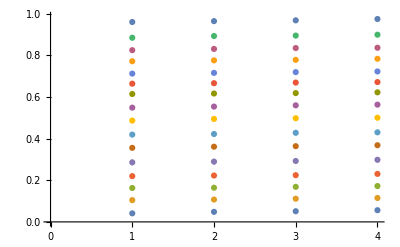

```mathematica
ListPlot[test]
```

```mathematica
ShowFitModel[data_, model_,Xlabel_,Ylabel_, title_, dcol_, mcol_]:=
Show[
ListPlot[data, PlotStyle->{dcol},PlotLegends->{"data"}],
Plot[model[x],{x,MinVal[data,1],MaxVal[data,1]},PlotStyle->{mcol, Thick},
PlotLegends->{N[model[Xlabel],7]},PlotRange->All],
PlotLabel->title,
AxesLabel->{Xlabel, Ylabel}
];
ShowLogFitModel[data_, model_,Xlabel_,Ylabel_, title_, dcol_, mcol_]:=
Show[
ListPlot[data, PlotStyle->{dcol},PlotLegends->{Ylabel}],
Plot[model[x],{x,MinVal[data,1],MaxVal[data,1]},PlotStyle->{mcol, PointSize[0.5]},
PlotLegends->{N[FullSimplify[Exp[model[Log[x]]]],7]},PlotRange->All],
PlotLabel->title,
AxesLabel->{Xlabel, Ylabel}
];
```

```mathematica
ShowLogFitModelBin[data_,bins_, model_,Xlabel_,Ylabel_, title_, dcol_, mcol_]:=
ShowLogFitModel[DataWithErrors[data,1,bins], model,Xlabel,Ylabel, title, dcol, mcol];
```

```mathematica
ClearAll[NumericalVector];
```

```mathematica
NumericalVector[{}] = False;
```

```mathematica
NumericVector[X_] := And @@(NumericQ  /@ X);
```

```mathematica
NumericVector[{1,2,3}]
```

True

```mathematica
testP0=BinaryReadList[StringJoin["/Users/am10485/Downloads/ClusterDataGPU3.5e8/FDBins.pos.np"],"Real64"];
```

```mathematica
Length[testP0]
```

9437184

```mathematica
Length[testP0]/9
```

1048576

```mathematica
testP1 = ArrayReshape[testP0,{Length[testP0]/9,9}];
```

```mathematica
testP1[[;;10]]
```

{{79.,-37.0511,0.00249031,-1.30961,6.65985,-30.2679,9.1074,19.6716,0.00102788},{80.,-37.0423,0.00269321,3.09146,5.65301,-25.6765,6.19809,19.6708,0.00254805},{80.,-37.0393,0.000700362,1.21001,5.71869,-29.3531,6.19273,19.6704,0.0023382},{80.,-37.0375,0.000281742,-2.95787,6.46685,-34.7171,7.08438,19.6673,0.00277539},{80.,-37.0353,0.000975252,-6.11647,3.26839,-37.6957,3.26679,19.6693,0.00422344},{80.,-37.0327,0.000759641,-0.661525,6.1476,-32.1861,7.16255,19.6665,0.00351841},{80.,-37.0292,0.000524082,5.7356,3.96352,-22.1335,5.13682,19.6681,0.00536917},{80.,-37.0271,0.000974516,-2.40324,6.40072,-32.6765,7.67925,19.665,0.00426429},{80.,-37.0251,0.000518028,3.06648,7.11045,-26.5904,7.74396,19.6624,0.00382987},{80.,-37.0234,0.000681262,-5.30434,4.76965,-37.2745,5.93136,19.6683,0.00535847}}

```mathematica
testP1[[-10;;]]
```

{{80.,-2.28946,3.79351×10^-8,4.7924,6.1661,-24.6917,5.50386,19.6592,0.00533973},{80.,-2.28946,9.6716×10^-8,5.60464,3.01512,-24.7656,2.71437,19.6593,0.00625429},{80.,-2.28946,Indeterminate,5.14831,5.37237,-25.5214,6.70366,19.6631,0.00441451},{80.,-2.28946,1.19961×10^-7,5.86272,3.73824,-24.0897,4.62344,19.6606,0.00766855},{80.,-2.28946,8.04726×10^-8,8.09272,1.09883,-23.4093,2.70498,19.658,0.00542425},{80.,-2.28946,Indeterminate,5.63448,4.76442,-24.6374,4.99622,19.6594,0.00780381},{80.,-2.28946,Indeterminate,6.71203,2.79081,-22.1278,4.17532,19.6613,0.00801127},{80.,-2.28946,1.00367×10^-7,4.83477,5.14462,-26.2079,5.40614,19.6629,0.00569355},{80.,-2.28946,Indeterminate,3.5661,6.22347,-26.0212,5.66634,19.6643,0.00721161},{80.,-2.28946,8.48255×10^-8,4.64783,5.32865,-25.6138,5.46877,19.6608,0.00672703}}

```mathematica
testP=Select[testP1,NumericVector];
```

```mathematica
Dimensions[testP]
```

{692471,9}

```mathematica
testN0=BinaryReadList[StringJoin["/Users/am10485/Downloads/ClusterDataGPU3.5e8/FDBins.neg.np"],"Real64"];
```

```mathematica
Length[testN0]
```

9437184

```mathematica
Length[testN0]/9
```

1048576

```mathematica
testN1 = ArrayReshape[testN0,{Length[testN0]/9,9}];
```

```mathematica
testN=Select[testN1,NumericVector];
```

```mathematica
Dimensions[testN]
```

{692769,9}

```mathematica
DataAround[A_,B_]:= Around[#[[1]],#[[2]]]&/@Transpose[{A, B}];
```

```mathematica
DataAround[Range[10], Table[1,10]]
```

{1.01.0,2.01.0,3.01.0,4.01.0,5.01.0,6.01.0,7.01.0,8.01.0,9.01.0,10.01.0}

```mathematica
First /@{{1,2},{3,4}}
```

{1,3}

```mathematica
AllSamples = Join[Select[testP,#[[1]] >1&],Select[testN,#[[1]] >1&]];
```

```mathematica
Length[AllSamples]
```

1385240

```mathematica
MakeProbAllDS[samples_, name_,bins_]:=Block[{P,nums, cc,cs,dd,ds,oo,os,qq,qs,numtot,Tail,lint,data, weights},
{nums, cc,cs,dd,ds,oo,os,qq,qs} = Transpose[Sort[samples, #1[[4]] < #2[[4]]&]];
numtot = Plus@@ nums ;
data =Transpose[{dd,Log[1-Accumulate[nums]/(1+numtot)]}];
ListPlot[DataWithErrors[data,bins],PlotStyle->Red, PlotLegends->{"DS"}]
]
```

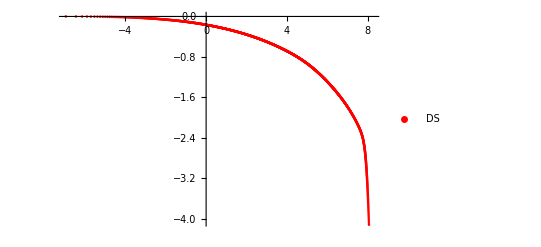

```mathematica
SHDS=MakeProbAllDS[AllSamples, "DS", 1000]
```

```mathematica
FitProbAllDS[samples_, numpol_, bins_]:=Block[{P,nums, cc,cs,dd,ds,oo,os,qq,qs,n0,n1,numtot,Tail,lint,data,wdata,weights, model},
{nums, cc,cs,dd,ds,oo,os,qq,qs} = Transpose[Sort[samples, #1[[4]] < #2[[4]]&]];
numtot = Plus@@ nums ;
data =Transpose[{dd,Log[1-Accumulate[nums]/(1+numtot)]}];
{n0, n1} = {Floor[0.01Length[dd]],Floor[0.99Length[dd]]};
{wdata, weights} = Transpose[DataWithWeights[data[[n0;;n1]],bins]];
model = LinearModelFit[wdata,
Table[ChebyshevT[n,2(x-wdata[[1,1]])/(wdata[[-1,1]]-wdata[[1,1]])-1],{n,0,numpol}],x,
Weights->First/@weights];
{wdata[[1,1]],wdata[[-1,1]], model}
]
```

```mathematica
{d0, d1, model} =FitProbAllDS[AllSamples,15, 1000];
```

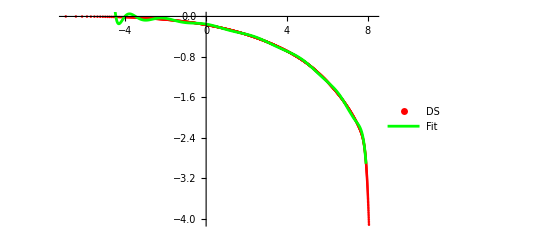

```mathematica
Show[{SHDS,Plot[model[x],{x,d0,d1}, PlotStyle->Green, PlotLegends->{"Fit"}]}]
```

```mathematica
FractalMom[T_,ξ0_, ξ1_] := Block[{ξ, L1},
L1= (x + T[x])/.FindRoot[1+T'[x],{x, (ξ0 + ξ1)/2}][[1]];
ParametricPlot[{- T'[ξ],( T[ξ] - ξ T'[ξ] + Log[-T'[ξ]])/L1}, {ξ, ξ0, ξ1},
AxesLabel->{n, η[n]}]
]
```

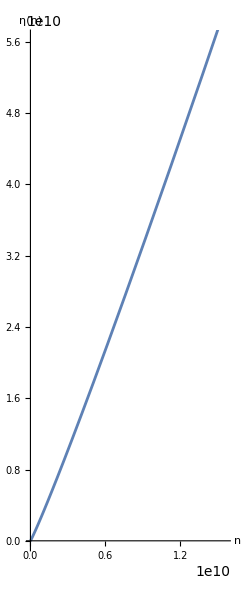

```mathematica
FractalMom[model,-20,-7]
```

```mathematica
MakeProbAllOO[samples_, name_, bins_]:=Block[{P,nums, cc,cs,dd,ds,oo,os,numtot,Tail,lint,data, weights},
{nums, cc,cs,dd,ds,oo,os, qq,qs} = Transpose[Sort[samples, #1[[6]] < #2[[6]]&]];
numtot = Plus@@ nums ;
data =Transpose[{oo,Log[1-Accumulate[nums]/(1+numtot)]}];
ListPlot[DataWithErrors[data,bins],PlotStyle->Blue, PlotLegends->{"OO"}]
]
```

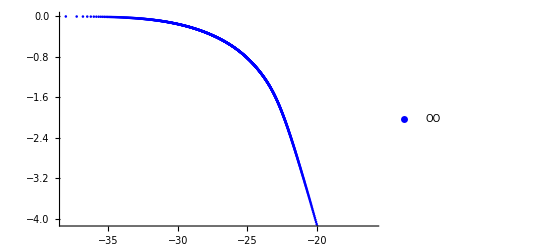

```mathematica
SHOO =MakeProbAllOO[AllSamples,"|ω.ω|/q^2",1000]
```

```mathematica
PlotOvsQvsK[samples_, bins_]:=Block[{Q,nums, dd,ds,oo,os,qq,qs,SP, SN,data,weights,numtot,Tail,lm},
{nums, cc,cs,dd,ds,oo,os,qq,qs} = Transpose[Sort[samples, #1[[6]] < #2[[6]]&]];
numtot = Plus@@ nums ;
(*data= Transpose[{oo,dd,Log[Accumulate[nums]/(1+numtot)]}];*)
data =Transpose[{oo,qq,dd}];
data = Mean[#]& /@Partition[data,bins];
ListLinePlot3D[data, Mesh->None , PlotStyle->Pink,AxesLabel->{"Log[|ω.ω|/q^2]","Log[q]","Log[ k Sqrt[ν t]]"}]
];
```

```mathematica
plt =PlotOvsQvsK[AllSamples, 1000]
```

-Graphics3D-

```mathematica
DataOvsQvsK[samples_, bins_]:=Block[{Q,nums, dd,ds,oo,os,qq,qs,SP, SN,data,weights,numtot,Tail,lm},
{nums, cc,cs,dd,ds,oo,os,qq,qs} = Transpose[Sort[samples, #1[[6]] < #2[[6]]&]];
data =Transpose[{oo,qq,dd}];
If[bins >1,data = Mean[#]& /@Partition[data,bins]];
data
];
```

```mathematica
data = DataOvsQvsK[AllSamples,100];
```

```mathematica
{oo,qq,dd} = Transpose[data];
```

```mathematica
Dimensions[Transpose[{oo,qq}]]
```

{13852,2}

```mathematica
Dimensions[dd]
```

{13852}

```mathematica
Transpose[{oo,qq}][[;;3]]
```

{{-38.4588,19.4065},{-38.1205,19.3732},{-37.9151,19.3123}}

```mathematica
lmo = NonlinearModelFit[data,{a +5/3 q +y},{a},{y,q}]
```

FittedModel[-1.48835+(5 q)/3+y]

```mathematica
Rationalize[1.6360045066201618,0.01 ]
```

18/11

```mathematica
Rationalize[0.993648985912535,0.01 ]
```

1

```mathematica
lmo["ParameterTable"]
```

General::munfl: Exp[-35935.6] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -1.48835 | 0.000947516 | -1570.79 | 0.

```mathematica
Exp[lmo[Log[y],Log[q]]]//FullSimplify
```

0.225745 q^(5/3) y

```mathematica
(1.46-1.488)/Log[3.5/3]
```

-0.18164

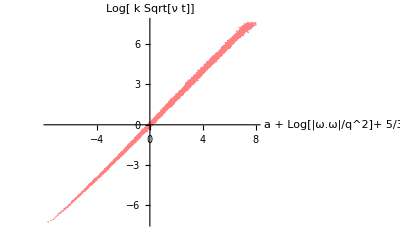

```mathematica
dataPlot =ListPlot[{lmo[#[[1]],#[[2]]],#[[3]]}&/@data,PlotStyle->Pink,AxesLabel->{"a +  Log[|ω.ω|/q^2]+ 5/3 Log[q]","Log[ k Sqrt[ν t]]"}]
```

```mathematica
3/2 5/3
```

5/2

```mathematica
N[-5/3 +1.6658505831098946]
```

-0.000816084

```mathematica
With[{b = 1.6658505831098946}, Zeta[3b/2-1]/Zeta[3b/2]]
```

1.95028

```mathematica
ListPlot3D[Flatten[Table[{n,q,q^(5/3)/n^2},{n,1,100},{q,2,200,2}],1],
InterpolationOrder->0,Mesh->None,AxesLabel->{n,q,κ}]
```

-Graphics3D-

```mathematica
Phi[n_] := Sum[EulerPhi[k],{k,1,n}]
```

```mathematica
Phi[1]
```

1

```mathematica
PhiT = Accumulate[ParallelTable[EulerPhi[n],{n, 100000}]];
```

```mathematica
PhiF[x_] := If[x < 1,0,If[ x > 100000,6 x^2/Pi^2,PhiT[[Floor[x]]]]];
```

```mathematica
PhiF[10000]
```

30397486

```mathematica
EE[z_, M_]:=1/Sqrt[z]Sum[N[EulerPhi[q]PhiF[Floor[q^(5/6)/Sqrt[z]]]/q^(25/6)],{q,2,M,2}];
```

```mathematica
EE[1,1000]
```

0.131256

```mathematica
Etab = ParallelTable[EE[z,10000],{z,1,1000,1}];
```

```mathematica
ListLogLogPlot[Etab,
PlotStyle->{Red,PointSize[0.003]},
PlotLabel->"Log-Log Energy Spectrum",
AxesLabel->{k Sqrt[ν t],"E[k,t]"}]
```

ListLogLogPlot::lpn: Etab is not a list of numbers or pairs of numbers.

ListLogLogPlot[Etab,PlotStyle→{RGBColor[1, 0, 0],PointSize[0.003]},PlotLabel→Log-Log Energy Spectrum,AxesLabel→{k √(t ν),E[k,t]}]

```mathematica
Phi2T = Accumulate[ParallelTable[EulerPhi[n]/n^2,{n,1,200000}]];
```

```mathematica
PPP[x_] := If[x <1,0,If[x > 200000,Phi2T[[200000]]Log[x]/Log[200000],Phi2T[[Floor[x]]]]];
```

```mathematica
PPP[17.5]
```

15299527769557/6254891042400

```mathematica
PPP[-2.5]
```

0

```mathematica
N[PPP[200001]]
```

8.11781

```mathematica
N[PPP[200000]]
```

8.1178

```mathematica
ET[T_, M_] := 1/T Sum[N[EulerPhi[q]/q^(25/6) PPP[q^(5/6)/T^(1/4)]],{q,2,M,2}];
```

```mathematica
ET[1,10000]
```

0.0694275

```mathematica
ETTab = Table[{T,ET[T, 10000]},{T,1,100,1}];
```

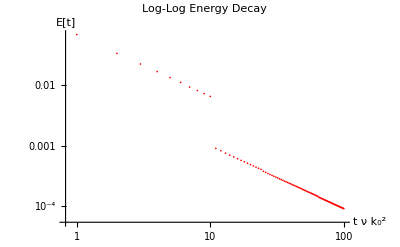

```mathematica
EPlt =ListLogLogPlot[ETTab,
PlotStyle->{Red,PointSize[0.003]},
PlotLabel->"Log-Log Energy Decay",
AxesLabel->{Subscript[k,0]^2 ν t,"E[t]"}]
```

```mathematica
ETTab1 = Table[{T,ET[T, 10000]},{T,100,1000,10}];
```

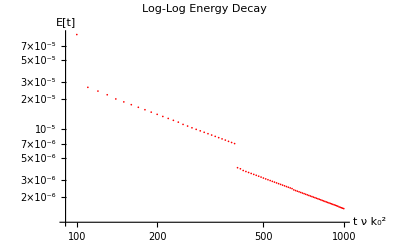

```mathematica
EPlt1 =ListLogLogPlot[ETTab1,
PlotStyle->{Red,PointSize[0.003]},
PlotLabel->"Log-Log Energy Decay",
AxesLabel->{Subscript[k,0]^2 ν t,"E[t]"}]
```

```mathematica
ETTab2 = Table[{T,ET[T, 10000]},{T,1000,10000,100}];
```

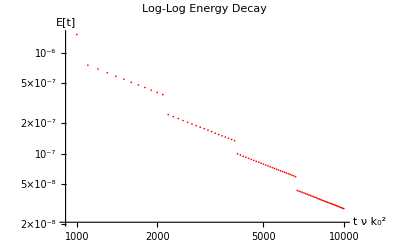

```mathematica
EPlt2 =ListLogLogPlot[ETTab2,
PlotStyle->{Red,PointSize[0.003]},
PlotLabel->"Log-Log Energy Decay",
AxesLabel->{Subscript[k,0]^2 ν t,"E[t]"}]
```

```mathematica
ETTab3= Table[{T,ET[T, 10000]},{T,10000,100000,1000}];
```

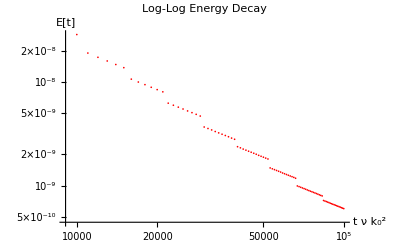

```mathematica
EPlt3 =ListLogLogPlot[ETTab3,
PlotStyle->{Red,PointSize[0.003]},
PlotLabel->"Log-Log Energy Decay",
AxesLabel->{Subscript[k,0]^2 ν t,"E[t]"}]
```

```mathematica
ETTab4= Table[{T,ET[T, 10000]},{T,100000,1000000,10000}];
```

$Aborted

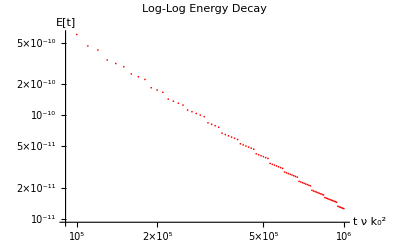

```mathematica
EPlt4 =ListLogLogPlot[ETTab4,
PlotStyle->{Red,PointSize[0.003]},
PlotLabel->"Log-Log Energy Decay",
AxesLabel->{Subscript[k,0]^2 ν t,"E[t]"}]
```

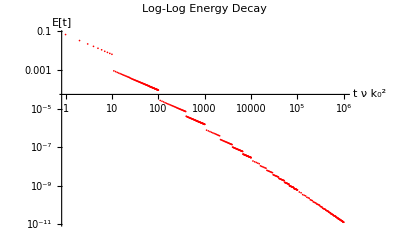

```mathematica
Show[{EPlt,EPlt1,EPlt2,EPlt3,EPlt4}, PlotRange->All]
```

```mathematica
data4 = Log[ETTab4];
```

```mathematica
data4[[;;10]]
```

{{Log[100000],-21.2337},{Log[110000],-21.4866},{Log[120000],-21.5777},{Log[130000],-21.7998},{Log[140000],-21.8773},{Log[150000],-21.9494},{Log[160000],-22.1088},{Log[170000],-22.1714},{Log[180000],-22.2315},{Log[190000],-22.4144}}

```mathematica
data4[[-1]]
```

{Log[1000000],-25.0998}

```mathematica
mod4 =NonlinearModelFit[data4,{α + β x},{α, β},x]
```

FittedModel[-2.34717-1.64698 x]

```mathematica
mod4["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
α | -2.34717 | 0.0623545 | -37.6424 | 1.88037×10^-56
β | -1.64698 | 0.00476698 | -345.497 | 5.47184×10^-141

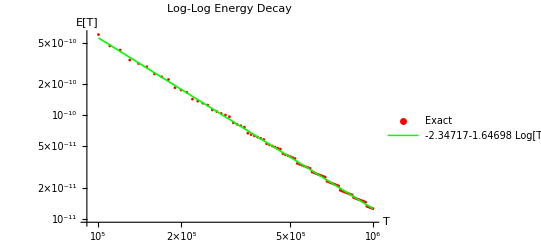

```mathematica
Show[{ListLogLogPlot[ETTab4,
PlotStyle->{Red,PointSize[0.005]},
PlotLabel->"Log-Log Energy Decay",
AxesLabel->{T,"E[T]"},
PlotLegends->{"Exact"}
],
Plot[mod4[x],{x,data4[[1]][[1]], data4[[-1]][[1]] }, 
PlotStyle->{Green, Thickness[0.003]},PlotLegends->{ mod4[Log[T]]}]}]
```

```mathematica
Slope[S1_,S2_] := (S1[[2]]- S2[[2]])/(S2[[1]]- S1[[1]]);
```

```mathematica
Slope[data4[[10]] ,data4[[15]] ]
```

1.4731

```mathematica
Slopes = Sort[Flatten[Table[Slope[data4[[i]] ,data4[[j]] ],{j,2,Length[data4]},{i,1,j-1}]]];
```

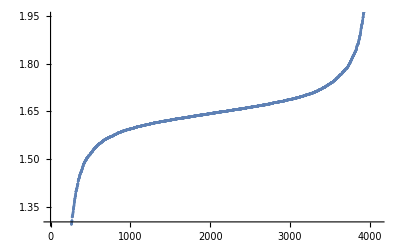

```mathematica
ListPlot[Slopes]
```

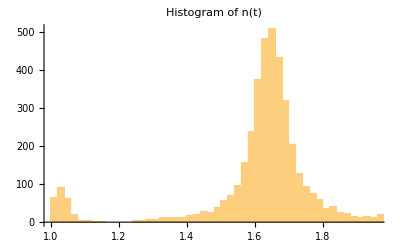

```mathematica
Histogram[Slopes,300,PlotLabel->"Histogram of n(t)"]
```

```mathematica
data3= Log[ETTab3];
```

```mathematica
Slopes3 = Sort[Flatten[Table[Slope[data3[[i]] ,data3[[j]] ],{j,2,Length[data3]},{i,1,j-1}]]];
```

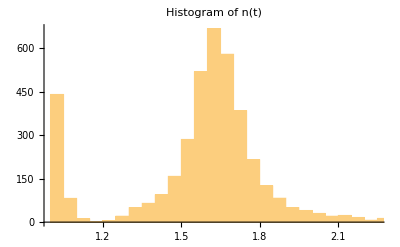

```mathematica
Histogram[Slopes3,PlotLabel->"Histogram of n(t)"]
```

```mathematica
Mean[Slopes]
```

1.64741

```mathematica
StandardDeviation[Slopes]
```

0.322147

```mathematica
10^(1.8)
```

63.0957

```mathematica
1/(19/6-1) Sum[EulerPhi[n]/n^(19/5),{n,1,Infinity}]
```

(6 Zeta[14/5])/(13 Zeta[19/5])

```mathematica
EE[n_] := (6 Zeta[14/5])/(13 Zeta[19/5])EulerPhi[n]/n^4
```

```mathematica
EED = ParallelTable[N[{n^(5/3),EE[n]}],{n,100,100000}];
```

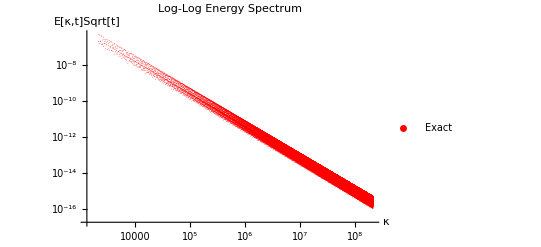

```mathematica
ListLogLogPlot[EED,PlotStyle->{Red,PointSize[0.001]},
PlotLabel->"Log-Log Energy Spectrum",
AxesLabel->{κ,"E[κ,t]Sqrt[t]"},
PlotLegends->{"Exact"}]
```

```mathematica
ET[n_] := (3 Zeta[18/5])/(4 Zeta[13/5])EulerPhi[n]/n^(17/3)
```

```mathematica
ETD = ParallelTable[N[{n^(10/3),ET[n]}],{n,100,100000}];
```

```mathematica
Dimensions[ETD]
```

{99901,2}

```mathematica
ETD[[;;10]]
```

{{4.64159×10^6,1.19036×10^-10},{4.79812×10^6,2.81275×10^-10},{4.95831×10^6,8.51205×10^-11},{5.12221×10^6,2.56729×10^-10},{5.28986×10^6,1.14377×10^-10},{5.46132×10^6,1.0834×10^-10},{5.63663×10^6,1.1123×10^-10},{5.81584×10^6,2.14989×10^-10},{5.999×10^6,6.92659×10^-11},{6.18617×10^6,1.97223×10^-10}}

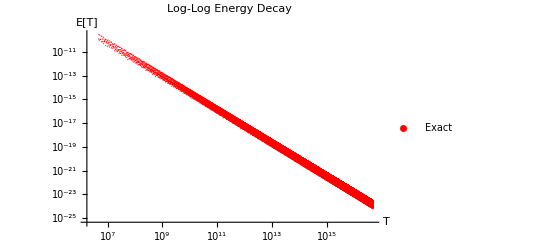

```mathematica
ListLogLogPlot[ETD,PlotStyle->{Red,PointSize[0.002]},
PlotLabel->"Log-Log Energy Decay",
AxesLabel->{T,"E[T]"},
PlotLegends->{"Exact"}]
```

```mathematica
dataETD = Log[ETD];
```

```mathematica
step = 200;
```

```mathematica
Slope[dataETD[[step]] ,dataETD[[2* step]] ]
```

1.32825

```mathematica
SlopesETD =Select[Sort[Flatten[ParallelTable[Slope[dataETD[[i]] ,dataETD[[j]] ],{j,2*step,Length[dataETD]-step,step},{i,step,j-step,step}]]],Positive];
```

```mathematica
Length[SlopesETD]
```

121000

```mathematica
SlopesETD[[;;10]]
```

{0.000290251,0.000294243,0.000482527,0.000486323,0.000981143,0.00139728,0.00143893,0.00149829,0.00172807,0.00176842}

```mathematica
SlopesETD[[-10;;]]
```

{143.069,146.721,150.12,150.66,152.078,154.024,154.29,154.439,157.676,219.791}

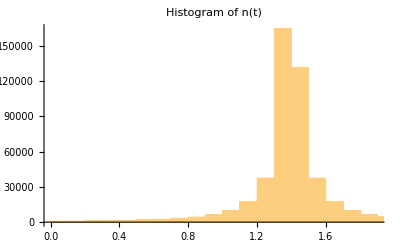

```mathematica
Histogram[SlopesETD,2500,PlotLabel->"Histogram of n(t)"]
```

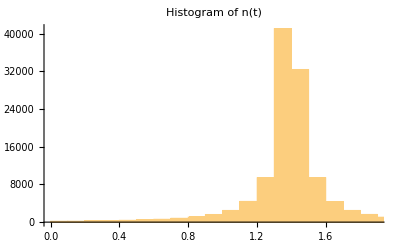

```mathematica
Histogram[SlopesETD,1000,PlotLabel->"Histogram of n(t)"]
```

```mathematica
StandardDeviation[Table[N[EulerPhi[n]/n - 6/Pi^2],{n, 1000000, 2000000}]]
```

0.242228

```mathematica
Prime[1]
```

2

```mathematica
S2=1/3NProduct[With[{p = Prime[n]},(1-2/p^2)(1 + 1/(p(p^2-2)))],{n,1,Infinity}]
```

Prime::intpp: Positive integer argument expected in Prime[15.].

Prime::intpp: Positive integer argument expected in Prime[14.].

Prime::intpp: Positive integer argument expected in Prime[13.].

General::stop: Further output of Prime::intpp will be suppressed during this calculation.

0.142987

```mathematica
R[M_] := N[Sum[EulerPhi[q]^2,{q,1,M}] /M^3];
```

```mathematica
R[10000000]
```

0.142748

```mathematica
Sqrt[S2 /(3 /Pi^2)^2 -1]N^(3/2)/N^2
```

0.739987/(√N)

```mathematica
PTBL1 = Table[With[{p = Prime[n]}, {p,N[(p-1)/EulerPhi[p+1]]}], {n,100000,1000000, 1000}];
```

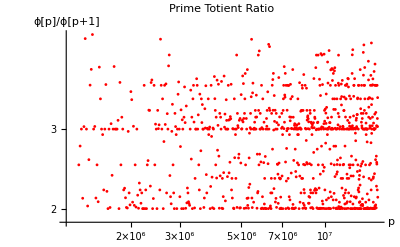

```mathematica
ListLogLogPlot[PTBL1,PlotStyle->{Red,PointSize[0.005]},
PlotLabel->"Prime Totient Ratio",
AxesLabel->{p,"ϕ[p]/ϕ[p+1]"}]
```

```mathematica
PTBL2 = Table[With[{p = Prime[n]}, {p,EulerPhi[p-1]/(p-1)}], {n,1000000}];
```

```mathematica
ListLogLogPlot[PTBL2,Plo]
```

-Graphics-

```mathematica
PTBL3 = ParallelTable[With[{p =n!}, {p,N[EulerPhi[p+1]/EulerPhi[p]]}], {n,50}];
```

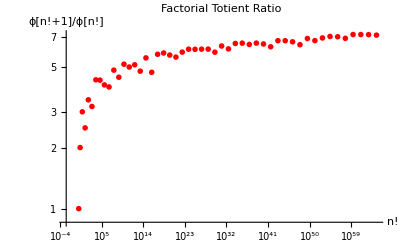

```mathematica
ListLogLogPlot[PTBL3,
PlotStyle->{Red,PointSize[0.01]},
PlotLabel->"Factorial Totient Ratio",
AxesLabel->{n!,"ϕ[n!+1]/ϕ[n!]"}]
```

```mathematica
PTBL4 = Table[With[{p = Prime[n]}, {p,Pi^2/(6 p)EulerPhi[p+1]}], {n,10000,1000000}];
```

```mathematica
ListLogLogPlot[PTBL4]
```

-Graphics-

```mathematica
PTBL5 = Table[ {p,Pi^2/(6 p)EulerPhi[p+1]}, {p,Prime[10000],Prime[1000000], 1000}];
```

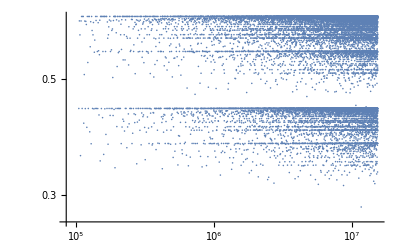

```mathematica
ListLogLogPlot[PTBL5]
```

```mathematica
PTBL6 = ParallelTable[With[{p =n!}, {p,N[EulerPhi[p+1]-EulerPhi[p]]}], {n,50}];
```

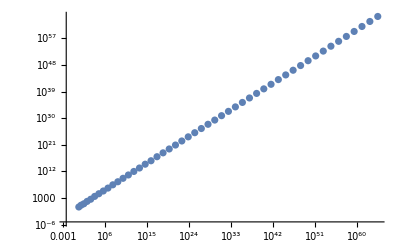

```mathematica
ListLogLogPlot[PTBL6]
```

```mathematica
With[{p= 2^64},N[Pi^2/(6 p)EulerPhi[p]]]
```

0.822467

```mathematica
With[{p= 2^64},N[Pi^2/(6 p)EulerPhi[p+1]]]
```

1.64493

```mathematica
N[2^(-64)]
```

5.42101×10^-20

```mathematica
EulerPhi[31]
```

30

```mathematica
TBL =Table[{n,EulerPhi[n]/(n-1)},{n,2,10000}];
```

```mathematica
PR =Select[TBL,PrimeQ[#[[1]]]&];
```

```mathematica
NPR = Select[TBL,!PrimeQ[#[[1]]]&];
```

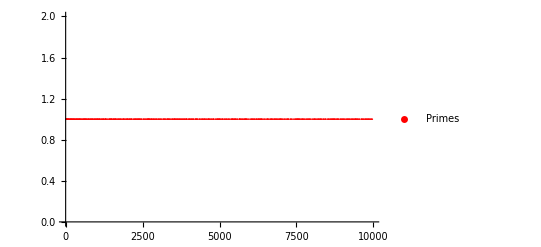

```mathematica
P1 =ListPlot[PR,
PlotStyle->{Red,PointSize[0.002]},
 PlotLegends->{"Primes"}]
```

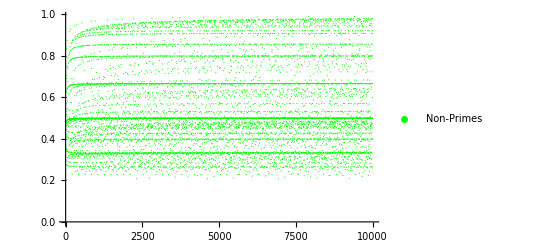

```mathematica
P2 =ListPlot[NPR,PlotStyle->{Green,PointSize[0.002]}, PlotLegends->{"Non-Primes"}]
```

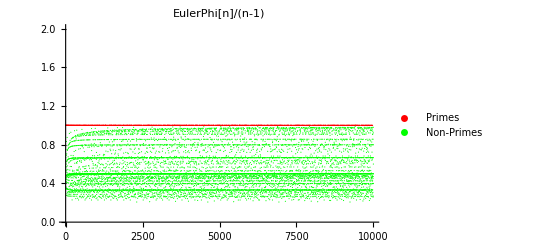

```mathematica
Show[{P1, P2},PlotLabel->"EulerPhi[n]/(n-1)"]
```

```mathematica
TBL1 =Table[{n,EulerPhi[n]/EulerPhi[n-1]},{n,2,10000}];
```

```mathematica
PR1 =Select[TBL1,PrimeQ[#[[1]]]&];
NPR1 = Select[TBL1,!PrimeQ[#[[1]]]&];
```

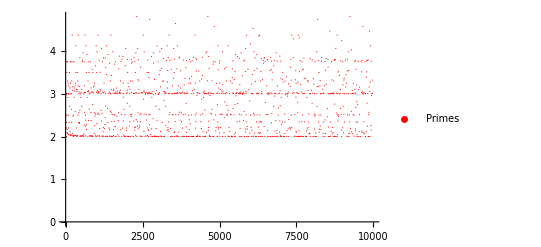

```mathematica
P11 =ListPlot[PR1,
PlotStyle->{Red,PointSize[0.002]},
 PlotLegends->{"Primes"}]
```

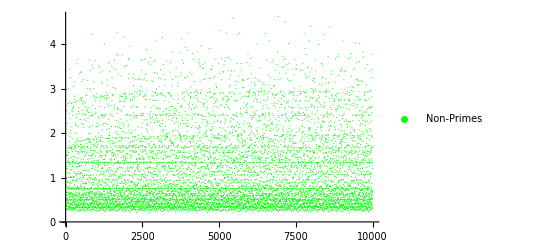

```mathematica
NP12 =ListPlot[NPR1,PlotStyle->{Green,PointSize[0.002]}, PlotLegends->{"Non-Primes"}]
```

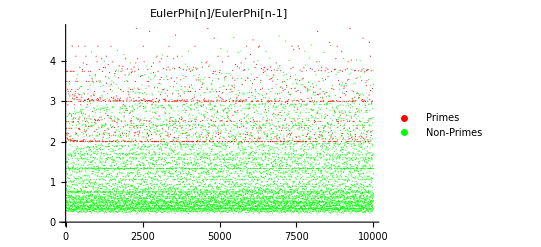

```mathematica
Show[{P11, NP12},PlotLabel->"EulerPhi[n]/EulerPhi[n-1]"]
```

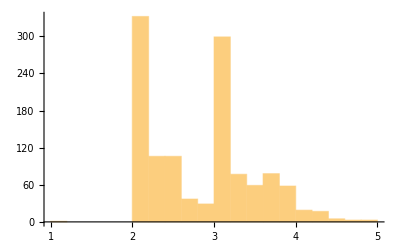

```mathematica
H1 = Histogram[#[[2]] &/@PR1]
```

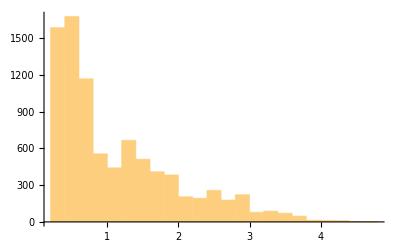

```mathematica
H2 = Histogram[#[[2]] &/@NPR1]
```

```mathematica
H12 = PairedHistogram[#[[2]] &/@PR1,#[[2]] &/@NPR1]
```

-Graphics-

```mathematica
Zeta[-2]
```

0

```mathematica
Zeta[-1]
```

-1/12

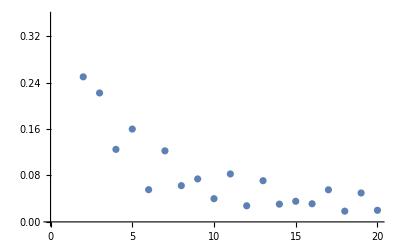

```mathematica
ListPlot[Table[EulerPhi[n]/n^2,{n,1,20}]]
```

```mathematica
EulerPhi[2]/2^2
```

1/4

```mathematica
EulerPhi[3]/3^2
```

2/9

```mathematica
data =ParallelTable[With[{q = Floor[(T 2^4)^(3/10)]},{T,EulerPhi[q]/(4 q^(10/3))} ],{T,1000,2000,1}];
```

```mathematica
data[[;;4]]
```

{{1000.,1/(3888 2^(1/3) 3^(2/3))},{1000.,1/(3888 2^(1/3) 3^(2/3))},{1000.,1/(3888 2^(1/3) 3^(2/3))},{1000.,1/(3888 2^(1/3) 3^(2/3))}}

```mathematica
N[Sort[data, #1[[2]] < #2[[2]]&][[-5;;]]]
```

{{1148.,0.000245867},{1147.,0.000245867},{1146.,0.000245867},{1145.,0.000245867},{1144.,0.000245867}}

```mathematica
Δ Subscript["E",2][T]
```

Δ E_2[T]

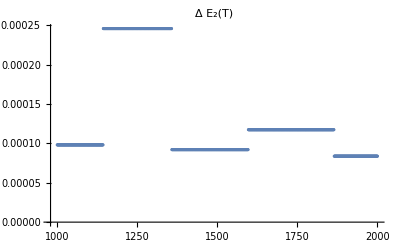

```mathematica
ListPlot[data,PlotLabel->Δ Subscript["E",2][T],PlotRange->All]
```

```mathematica
data3 =ParallelTable[With[{q = Floor[(T 3^4)^(3/10)]},{T,2EulerPhi[q]/(9q^(10/3))} ],{T,1000,2000,1}];
```

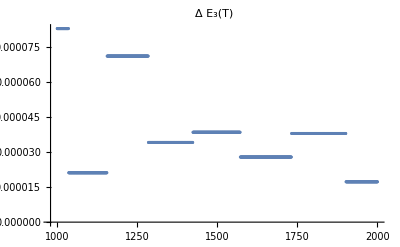

```mathematica
ListPlot[data3,PlotLabel->Δ Subscript["E",3][T],PlotRange->All]
```

```mathematica
TotData = ParallelTable[N[EulerPhi[n]/(n-1)],{n,1000000,2000000}];
```

```mathematica
Max[TotData]
```

1.

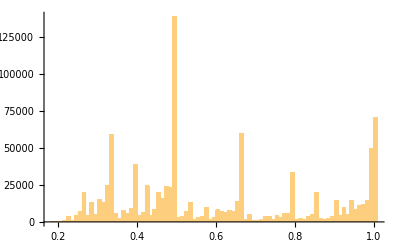

```mathematica
SH=Histogram[TotData,100,ChartLegends->"PDF[ϕ[n]/n]"]
```

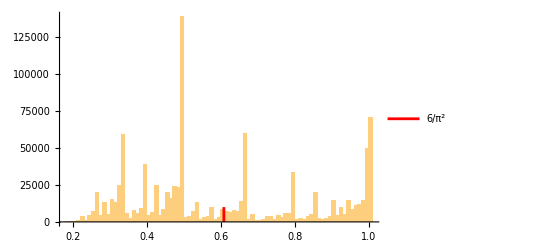

```mathematica
Show[{SH,ParametricPlot[{6/Pi^2,t},{t,0,10000},PlotStyle->Red,PlotLegends->{6/Pi^2}]}]
```

```mathematica
N[EulerPhi[2^64]/(2^64-1)]
```

0.5

```mathematica
N[EulerPhi[2^64+1]/(2^64)]
```

0.999996

```mathematica
N[6/Pi^2]
```

0.607927